```mathematica
SetDirectory["/project/theorie/h/H.Guertner/BEC_Polaron/Mathematica/"];
<< params.mx;
SetDirectory[ParentDirectory[]];
p =Import["DiagMC_BEC.json", {"Data", "Momentum"} ];
μ = Import["DiagMC_BEC.json", {"Data", "Chemical_Potential"} ];
```

```mathematica
peter=Import["/home/h/H.Guertner/theorie/BEC_Polaron/peter/FP_all", "Table"];
peter1=Import["/home/h/H.Guertner/theorie/BEC_Polaron/peter/FP_1", "Table"];
data=Import["data/without_measreweight/all_orders", "Table"];
data1= Import["data/without_measreweight/first_order", "Table"];
data1 = Insert [data1, {0,0,0}, 1];
```

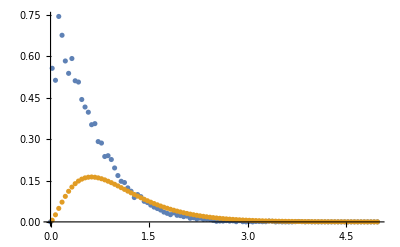

```mathematica
ListPlot[{data1[[All,1;;2]], peter1[[All,1;;2]]}, PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.000444889} lies outside the range of data in the interpolating function. Extrapolation will be used.

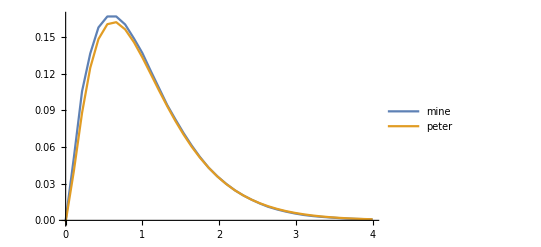

```mathematica
mygose1= Interpolation[data1[[All,1;;2]]];
myg1[tau_] := NIntegrate[mygose1[t]*g0[p, t, tau], {t,0,tau}];
g1= Interpolation[peter1[[All,1;;2]]];
Plot [{myg1[t], g1[t]}, {t,0,4}, PlotPoints->10, MaxRecursion->2, PlotRange->Full, PlotLegends->{"mine", "peter"}]
```